```mathematica
(*Set your directory to where the mathematica notebook is saved*)
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Import simulated data sets for K=2 (data1), K=3 (data2), K=4 (data3), K=5 (data4) *)
data1=Import["data/K2FM9E-06DMk0.05A.voc","Table","FieldSeparators"->","];
data2=Import["data/K3FM9E-06DMk0.05A.voc","Table","FieldSeparators"->","];
data3=Import["data/K4FM2E-05DMk0.2A.voc","Table","FieldSeparators"->","];
data4=Import["data/K5FM2E-05DMk0.2A.voc","Table","FieldSeparators"->","];
```

## Figure 5A

```mathematica
(*For visual purposes, for any simulation run where Subscript[T, i:(i+1)] is infinity (i.e., the (i+1)^th VOC lineage is not produced by the end of the simulation period), we set infinity to be equal to 800*)
genTime=5.2;
infinity=800;
temp={};
deltaMax=infinity/genTime;

totalLineage3={};
totalLineageTimetoFirst3={};
For[i=2,i≤Length[data3],i++,
AppendTo[totalLineage3,Length[data3[[i]]]-1];
AppendTo[totalLineageTimetoFirst3,{Length[data3[[i]]]-1,genTime data3[[i,2]]}]];

(*If total number of lineages is below 1000, it means that some of the runs generated zero VOCs.*)
If[Length[totalLineage3]<1000,totalLineage3=Join[totalLineage3,ConstantArray[0,1000-Length[totalLineage3]]]];

timeBetweenLineage3={};
For[i=2,i≤Length[data3],i++,
If[Length[data3[[i]]]≥2,temp={};
AppendTo[temp,data3[[i,2]]];
For[j=3,j≤Length[data3[[i]]],j++,
AppendTo[temp,data3[[i,j]]-data3[[i,j-1]]]],AppendTo[temp,deltaMax]];
AppendTo[timeBetweenLineage3,temp]];

(*If the (i+1)^th VOC lineage is not produced by the end of the simulation period, set  Subscript[T, i:(i+1)] to infinity*)
For[i=1,i≤Length[timeBetweenLineage3],i++,If[Length[timeBetweenLineage3[[i]]]<5,timeBetweenLineage3[[i]]=Join[timeBetweenLineage3[[i]],ConstantArray[deltaMax,5-Length[timeBetweenLineage3[[i]]]]]]];

gaps3=ConstantArray[{},Max[totalLineage3]];
For[i=1,i≤Length[timeBetweenLineage3],i++,
For[j=1,j≤Length[timeBetweenLineage3[[i]]],j++,
If[timeBetweenLineage3[[i,j]]==deltaMax,AppendTo[gaps3[[j]],deltaMax],AppendTo[gaps3[[j]],timeBetweenLineage3[[i,j]]]]]];

(*repeat the same for data2*)
totalLineage2={};
totalLineageTimetoFirst2={};
For[i=2,i≤Length[data2],i++,
AppendTo[totalLineage2,Length[data2[[i]]]-1];
AppendTo[totalLineageTimetoFirst2,{Length[data2[[i]]]-1,genTime data2[[i,2]]}]];

If[Length[totalLineage2]<1000,totalLineage2=Join[totalLineage2,ConstantArray[0,1000-Length[totalLineage2]]]];

timeBetweenLineage2={};
For[i=2,i≤Length[data2],i++,
If[Length[data2[[i]]]≥2,temp={};
AppendTo[temp,data2[[i,2]]];
For[j=3,j≤Length[data2[[i]]],j++,
AppendTo[temp,data2[[i,j]]-data2[[i,j-1]]]],AppendTo[temp,deltaMax]];
AppendTo[timeBetweenLineage2,temp]];

For[i=1,i≤Length[timeBetweenLineage2],i++,If[Length[timeBetweenLineage2[[i]]]<5,timeBetweenLineage2[[i]]=Join[timeBetweenLineage2[[i]],ConstantArray[deltaMax,5-Length[timeBetweenLineage2[[i]]]]]]];

gaps2=ConstantArray[{},Max[totalLineage2]];
For[i=1,i≤Length[timeBetweenLineage2],i++,
For[j=1,j≤Length[timeBetweenLineage2[[i]]],j++,
If[timeBetweenLineage2[[i,j]]==deltaMax,AppendTo[gaps2[[j]],deltaMax],AppendTo[gaps2[[j]],timeBetweenLineage2[[i,j]]]]]]

(*repeat the same for data1*)
totalLineage1={};
totalLineageTimetoFirst1={};
For[i=2,i≤Length[data1],i++,
AppendTo[totalLineage1,Length[data1[[i]]]-1];
AppendTo[totalLineageTimetoFirst1,{Length[data1[[i]]]-1,genTime data1[[i,2]]}]];

If[Length[totalLineage1]<1000,totalLineage1=Join[totalLineage1,ConstantArray[0,1000-Length[totalLineage1]]]];

timeBetweenLineage1={};
For[i=2,i≤Length[data1],i++,
If[Length[data1[[i]]]≥2,temp={};
AppendTo[temp,data1[[i,2]]];
For[j=3,j≤Length[data1[[i]]],j++,
AppendTo[temp,data1[[i,j]]-data1[[i,j-1]]]],AppendTo[temp,deltaMax]];
AppendTo[timeBetweenLineage1,temp]];

For[i=1,i≤Length[timeBetweenLineage1],i++,If[Length[timeBetweenLineage1[[i]]]<5,timeBetweenLineage1[[i]]=Join[timeBetweenLineage1[[i]],ConstantArray[deltaMax,5-Length[timeBetweenLineage1[[i]]]]]]];

gaps1=ConstantArray[{},Max[totalLineage1]];
For[i=1,i≤Length[timeBetweenLineage1],i++,
For[j=1,j≤Length[timeBetweenLineage1[[i]]],j++,
If[timeBetweenLineage1[[i,j]]==deltaMax,AppendTo[gaps1[[j]],deltaMax],AppendTo[gaps1[[j]],timeBetweenLineage1[[i,j]]]]]]


totalLineage4={};
totalLineageTimetoFirst4={};
For[i=2,i≤Length[data4],i++,
AppendTo[totalLineage4,Length[data4[[i]]]-1];
AppendTo[totalLineageTimetoFirst4,{Length[data4[[i]]]-1,genTime data4[[i,2]]}]];

If[Length[totalLineage4]<1000,totalLineage4=Join[totalLineage4,ConstantArray[0,1000-Length[totalLineage4]]]];

timeBetweenLineage4={};
For[i=2,i≤Length[data4],i++,
If[Length[data4[[i]]]≥2,temp={};
AppendTo[temp,data4[[i,2]]];
For[j=3,j≤Length[data4[[i]]],j++,
AppendTo[temp,data4[[i,j]]-data4[[i,j-1]]]],AppendTo[temp,deltaMax]];
AppendTo[timeBetweenLineage4,temp]];

For[i=1,i≤Length[timeBetweenLineage4],i++,If[Length[timeBetweenLineage4[[i]]]<5,timeBetweenLineage4[[i]]=Join[timeBetweenLineage4[[i]],ConstantArray[deltaMax,5-Length[timeBetweenLineage4[[i]]]]]]];

gaps4=ConstantArray[{},Max[totalLineage4]];
For[i=1,i≤Length[timeBetweenLineage4],i++,
For[j=1,j≤Length[timeBetweenLineage4[[i]]],j++,
If[timeBetweenLineage4[[i,j]]==deltaMax,AppendTo[gaps4[[j]],deltaMax],AppendTo[gaps4[[j]],timeBetweenLineage4[[i,j]]]]]];
```

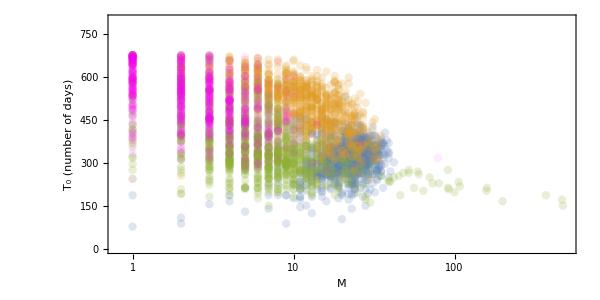

```mathematica
ListLogLinearPlot[{totalLineageTimetoFirst1,totalLineageTimetoFirst2,totalLineageTimetoFirst3,totalLineageTimetoFirst4},Frame->True,FrameLabel->{"M","T_0 (number of days)"},FrameStyle->Directive[Black,22],ImageSize->600,PlotTheme->"Detailed",PlotRange->{{0.8,500},{0,800}},PlotStyle->{{PointSize[.01],Opacity[0.2],ColorData[97,"ColorList"][[1]]},{PointSize[.01],Opacity[0.2],ColorData[97,"ColorList"][[2]]},{PointSize[.01],Opacity[0.2],ColorData[97,"ColorList"][[3]]},{PointSize[.01],Opacity[0.08],Magenta}},AspectRatio->1/2]
```

```mathematica
Histogram[{totalLineage1,totalLineage2,totalLineage3,totalLineage4},{0,Max[totalLineage3]+0.5,1},"Probability",Ticks->{Table[x,{x,Min[totalLineage3],Max[totalLineage3],1}],Automatic},ChartStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],Magenta},Frame->True,FrameLabel->{"Number of established VOC lineages, M","Frequency"},FrameStyle->Directive[Black,22],ImageSize->900,PlotRange->{{0,37},{0,0.23}},ChartLegends->{Style["K=2",24],Style["K=3",24],Style["K=4",24],Style["K=5",24]},AspectRatio->1/2]
```

## Figure 5B

```mathematica
points1={};
points2={};
points3={};
points4={};
repeat=999;
count=0;
maxX=600;
maxY=100;
scale=1000;
scalex=100;
genTime=5.2;
counter1=0;
counter2=0;
counter3=0;
counter4=0;

count=0;
For[i=2,i≤Length[data1],i++,
For[j=0,j≤repeat,j++,
If[data1⟦i,1⟧==j&&Length[data1⟦i⟧]≥4,AppendTo[points1,{genTime data1⟦i,2⟧, (genTime (data1⟦i,4⟧-data1⟦i,2⟧))/.(0.->0.2)}];count++;Break[]];
];
If[count==0,counter1++;AppendTo[points1,{maxX+scalex RandomReal[],5maxY+scale RandomReal[]}]];
count=0;
];
If[Length[data1]-1<1000,For[i=1,i≤1000-(Length[data1]-1),i++,counter1++;AppendTo[points1,{maxX+scalex RandomReal[],5maxY+scale RandomReal[]}]]];

count=0;
For[i=2,i≤Length[data2],i++,
For[j=0,j≤repeat,j++,
If[data2⟦i,1⟧==j&&Length[data2⟦i⟧]≥4,AppendTo[points2,{genTime data2⟦i,2⟧, (genTime (data2⟦i,4⟧-data2⟦i,2⟧))/.(0.->0.2)}];count++;Break[]];
];
If[count==0,counter2++;AppendTo[points2,{maxX+scalex RandomReal[],15maxY+scale RandomReal[]}]];
count=0;
];
If[Length[data2]-1<1000,For[i=1,i≤1000-(Length[data2]-1),i++,counter2++;AppendTo[points2,{maxX+scalex RandomReal[],15maxY+scale RandomReal[]}]]];

count=0;
For[i=2,i≤Length[data3],i++,
For[j=0,j≤repeat,j++,
If[data3⟦i,1⟧==j&&Length[data3⟦i⟧]≥4,AppendTo[points3,{genTime data3⟦i,2⟧, (genTime (data3⟦i,4⟧-data3⟦i,2⟧))/.(0.->0.2)}];count++;Break[]];
];
If[count==0,counter3++;AppendTo[points3,{maxX+scalex RandomReal[],50maxY+scale RandomReal[]}]];
count=0;
];
If[Length[data3]-1<1000,For[i=1,i≤1000-(Length[data3]-1),i++,counter3++;AppendTo[points3,{maxX+scalex RandomReal[],50maxY+scale RandomReal[]}]]];


count=0;
For[i=2,i≤Length[data4],i++,
For[j=0,j≤repeat,j++,
If[data4⟦i,1⟧==j&&Length[data4⟦i⟧]≥4,AppendTo[points4,{genTime data4⟦i,2⟧, (genTime (data4⟦i,4⟧-data4⟦i,2⟧))/.(0.->0.2)}];count++;Break[]];
];
If[count==0,counter4++;AppendTo[points4,{maxX+scalex RandomReal[],100maxY+10scale RandomReal[]}]];
count=0;
];
If[Length[data4]-1<1000,For[i=1,i≤1000-(Length[data4]-1),i++,counter4++;AppendTo[points4,{maxX+scalex RandomReal[],100maxY+10scale RandomReal[]}]]];

(*Print percentage of failed simulations*)
{counter1,counter2,counter3,counter4}/(repeat+1)*100.
```

{0.4,4.4,10.3,50.}

```mathematica
plot1=ListLogPlot[{points1,points2,points3,points4},PlotRange->{{0,730},{0.1,60000}},PlotStyle->{{PointSize[.01],Opacity[0.2],ColorData[97,"ColorList"][[1]]},{PointSize[.01],Opacity[0.2],ColorData[97,"ColorList"][[2]]},{PointSize[.01],Opacity[0.2],ColorData[97,"ColorList"][[3]]},{PointSize[.01],Opacity[0.2],Magenta}}];

(*enclosed red dashed line represents the acceptable range in the time for the emergence of Alpha, Beta, and Gamma VOCs*)
(*The cross sign shows the mean estimate for the emergence of Alpha (x-axis) and time between the emergence of Beta and Gamma (y-axis)*)
Needs["Calendar`"];
epilog={EdgeForm[Directive[Thick,Dashed,Red]],Transparent,Rectangle[{DaysBetween[{2020, 1, 3}, {2020, 7,15}],DaysBetween[{2020, 8, 31}, {2020, 10,6}]},{DaysBetween[{2020, 1, 3}, {2020, 11,24}],DaysBetween[{2020, 7, 15}, {2020, 11,24}]}]};
(*coordinates for the cross sign*)
c1=DaysBetween[{2020, 1, 3}, {2020, 9,15}];
c2=DaysBetween[{2020, 8, 7}, {2020, 11,15}];
plot2=ListLogPlot[{{c1,c2}},Epilog->(epilog/.{x_,y_?NumericQ}:>{x,Log[y]}),PlotMarkers->Style["X",{White,Bold,FontSize->25}],Frame->True,FrameLabel->{"Time to the establishment of the first VOC, T_0
(date)","Time between the emergence of the first and third VOC
(number of days)"},FrameStyle->{{Directive[Black,22],Directive[Black,22]},{Directive[Black,22],Directive[Black,18]}},ImageSize->900,FrameTicks->{{{{0.2,"0"},{1,"1"},{2,""},{3,""},{4,""},{5,""},{6,""},{7,""},{8,""},{9,""},{10,"10"},{20,""},{30,""},{40,""},{50,""},{60,""},{70,""},{80,""},{90,""},{100,"100"},{200,""},{300,""},{400,""},{500,"500"}},Automatic},{{{0,"2020-01-03"},{75,""},{150,"2020-06-01"},{225,""},{300,"2020-10-29"},{375,""},{450,"2021-03-28"},{525,""},{600,"2021-08-25"},{675,""}},Automatic}}];
plot3=ListLogPlot[{{c1,c2}},PlotMarkers->Style["X",{Red,Bold,FontSize->25}]];
```

```mathematica
(*for each simulation run, check whether they fall within the red enclosed line or not (i.e., whether they give rise to the clustered emergence of VOCs in late 2020*)
count1=0;
For[i=2,i≤Length[data1],i++,If[Length[data1⟦i⟧]≥4,x=genTime data1[[i,2]];y=genTime(data1[[i,4]]-data1[[i,2]]);If[DaysBetween[{2020, 1, 3}, {2020, 7,15}]≤x≤DaysBetween[{2020, 1, 3}, {2020, 11,24}]&&DaysBetween[{2020, 8, 31}, {2020, 10,6}]≤y≤DaysBetween[{2020, 7, 15}, {2020, 11,24}],count1++]]];
count2=0;
For[i=2,i≤Length[data2],i++,If[Length[data2⟦i⟧]≥4,x=genTime data2[[i,2]];y=genTime(data2[[i,4]]-data2[[i,2]]);If[DaysBetween[{2020, 1, 3}, {2020, 7,15}]≤x≤DaysBetween[{2020, 1, 3}, {2020, 11,24}]&&DaysBetween[{2020, 8, 31}, {2020, 10,6}]≤y≤DaysBetween[{2020, 7, 15}, {2020, 11,24}],count2++]]];
count3=0;
For[i=2,i≤Length[data3],i++,If[Length[data3⟦i⟧]≥4,x=genTime data3[[i,2]];y=genTime(data3[[i,4]]-data3[[i,2]]);If[DaysBetween[{2020, 1, 3}, {2020, 7,15}]≤x≤DaysBetween[{2020, 1, 3}, {2020, 11,24}]&&DaysBetween[{2020, 8, 31}, {2020, 10,6}]≤y≤DaysBetween[{2020, 7, 15}, {2020, 11,24}],count3++]]];
count4=0;
For[i=2,i≤Length[data4],i++,If[Length[data4⟦i⟧]≥4,x=genTime data4[[i,2]];y=genTime(data4[[i,4]]-data4[[i,2]]);If[DaysBetween[{2020, 1, 3}, {2020, 7,15}]≤x≤DaysBetween[{2020, 1, 3}, {2020, 11,24}]&&DaysBetween[{2020, 8, 31}, {2020, 10,6}]≤y≤DaysBetween[{2020, 7, 15}, {2020, 11,24}],count4++]]];
{count1,count2,count3,count4}/1000*100.
```

{31.5,2.3,16.8,0.6}

```mathematica
Show[plot2,plot1,plot3,PlotRange->All,AspectRatio->1/2]
```

```mathematica
(*In the paper, we manually added the bold green circule to highlight the selected simulation run panel C and percentage of failed runs in a box on the top right hand side of the figure*)
```

## Figure 5C

```mathematica
(*Import simulated trajectories*)
```

```mathematica
trajs=Import["data/trajectory/K4FM2E-05DMk0.2A.traj","Data"];
trajs=trajs[[2;;]];

(*Import VOC lineage trajectories*)
vocs=Import["data/trajectory/K4FM2E-05DMk0.2A.lineage"];
vocTrajs=Table[Table[{(ToExpression[StringSplit[vocs[[i,1]],","]][[3]]+j-1)*genTime,ToExpression[StringSplit[vocs[[i,1]],","]][[3+j]]},{j,1,Length[ToExpression[StringSplit[vocs[[i,1]],","]]]-3}],{i,2,Length[vocs]}];
Table[PrependTo[vocTrajs[[i]],{vocTrajs[[i,1,1]]-genTime,0.1}],{i,1,Length[vocTrajs]}];
```

```mathematica
(*plot VOC trajectories along with the rest of the population*)
vocplot=ListLogPlot[vocTrajs,Joined->True,Joined->True,PlotRange->{{0,genTime Length[Transpose[trajs][[1]]]},{0.05,Automatic}},ImageSize->900,PlotTheme->"Scientific",PlotRange->All,FrameStyle->Directive[Black,22],FrameLabel->{"Date","Number of individuals"},LabelStyle->Directive[Black,15],PlotLabel->Style["",18,Black,Bold],PlotStyle->{{White,Dashed}},FrameTicks->{{{{0.1,"0"},{1,"1"},{2,""},{3,""},{4,""},{5,""},{6,""},{7,""},{8,""},{9,""},{10,"10"},{20,""},{30,""},{40,""},{50,""},{60,""},{70,""},{80,""},{90,""},{100,"10^2"},{200,""},{300,""},{400,""},{500,""},{600,""},{700,""},{800,""},{900,""},{1000,"10^3"},{2000,""},{3000,""},{4000,""},{5000,""},{6000,""},{7000,""},{8000,""},{9000,""},{10000,"10^4"},{20000,""},{30000,""},{40000,""},{50000,""},{60000,""},{70000,""},{80000,""},{90000,""},{100000,"10^5"},{200000,""},{300000,""},{400000,""},{500000,""},{600000,""},{700000,""},{800000,""},{900000,""},{1000000,"10^6"},{2000000,""},{3000000,""},{4000000,""},{5000000,""},{6000000,""},{7000000,""},{8000000,""},{9000000,""},{10000000,"10^7"}},Automatic},{{{0,"     2020-01-03"},{75,""},{150,"2020-06-01"},{225,""},{300,"2020-10-29"},{375,""},{450,"2021-03-28"},{525,""},{600,"2021-08-25"}},Automatic}}];

op=0.8;
populationplot=ListLogPlot[Table[MapThread[List,{genTime Transpose[trajs][[2]],Transpose[trajs][[i]]/.(0->0.1)}],{i,3,18}],Joined->True,Joined->True,PlotRange->{{0,genTime Length[Transpose[trajs][[1]]]},{0.05,Automatic}},Filling->Axis,FillingStyle->Directive[Opacity[0.1]],PlotStyle->{{Gray,Opacity[op]},{Green,Opacity[op]},{Green,Opacity[op]},{Green,Opacity[op]},{Green,Opacity[op]},{Darker[Green],Opacity[op]},{Darker[Green],Opacity[op]},{Darker[Green],Opacity[op]},{Darker[Green],Opacity[op]},{Darker[Green],Opacity[op]},{Darker[Darker[Green]],Opacity[op]},{Darker[Darker[Green]],Opacity[op]},{Darker[Darker[Green]],Opacity[op]},{Darker[Darker[Green]],Opacity[op]},{Darker[Darker[Green]],Opacity[op]},{Darker[Darker[Darker[Green]]],Opacity[1]}},ImageSize->900,PlotTheme->"Scientific",FrameStyle->Directive[Black,22],FrameLabel->{"Date","Number of individuals"},LabelStyle->Directive[Black,15],PlotLabel->Style["",18,White,Thickness[0.008]],FrameTicks->{{{{0.1,"0"},{1,"1"},{2,""},{3,""},{4,""},{5,""},{6,""},{7,""},{8,""},{9,""},{10,"10"},{20,""},{30,""},{40,""},{50,""},{60,""},{70,""},{80,""},{90,""},{100,"10^2"},{200,""},{300,""},{400,""},{500,""},{600,""},{700,""},{800,""},{900,""},{1000,"10^3"},{2000,""},{3000,""},{4000,""},{5000,""},{6000,""},{7000,""},{8000,""},{9000,""},{10000,"10^4"},{20000,""},{30000,""},{40000,""},{50000,""},{60000,""},{70000,""},{80000,""},{90000,""},{100000,"10^5"},{200000,""},{300000,""},{400000,""},{500000,""},{600000,""},{700000,""},{800000,""},{900000,""},{1000000,"10^6"},{2000000,""},{3000000,""},{4000000,""},{5000000,""},{6000000,""},{7000000,""},{8000000,""},{9000000,""},{10000000,"10^7"}},Automatic},{{{0,"     2020-01-03"},{75,""},{150,"2020-06-01"},{225,""},{300,"2020-10-29"},{375,""},{450,"2021-03-28"},{525,""},{600,"2021-08-25"}},Automatic}}];

Show[populationplot,vocplot,AspectRatio->1/2]
```